# Math 223: Homework 1

Ali Heydari

Jan 28, 2021

```mathematica
Clear["Global`*"]
```

## Problem 1

Use the Series command to compute the Taylor series of (1 + (x))^(1/x) about x = 0. Explore different parameter values to make sure you understand how to use this command. Use the Plot command to plot a comparison of this function with the polynomial of degree 4 given by the partial sum of the Taylor series over the interval [−1, 4]

Computing the first 10 Taylor series terms about the point x=0

```mathematica
n = 10;
func = (1+x)^(1/x)
x0 = 0;
expansion1 = Series[func,{x,x0,n}]
```

10

(1+x)^(1/x)

0

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760-(959 ⅇ x^5)/2304+(238043 ⅇ x^6)/580608-(67223 ⅇ x^7)/165888+(559440199 ⅇ x^8)/1393459200-(123377159 ⅇ x^9)/309657600+(29128857391 ⅇ x^10)/73574645760+O[x]^11

Now to play get the 4th order Taylor polynomial:

```mathematica
n = 4
```

4

```mathematica
expansion2 = Series[func,{x,x0,n}]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760+O[x]^5

```mathematica
expansion2 = Normal[%]
```

ⅇ-(ⅇ x)/2+(11 ⅇ x^2)/24-(7 ⅇ x^3)/16+(2447 ⅇ x^4)/5760

Now to compare the actual function with the the Taylor polynomial of order 4:

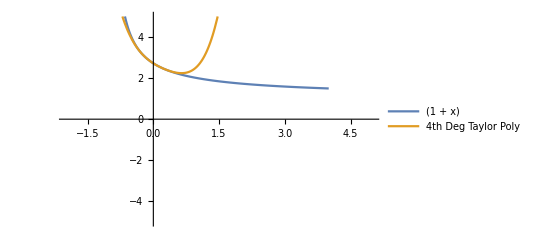

```mathematica
Plot[{func,expansion2},{x,-1,4},PlotRange->{{-2,5},{-5,5}}, PlotLegends->{"(1 + x)","4th Deg Taylor Poly"}]
```

And the plot makes sense, since we see the expansion roughly match the function around the expanded point.

## Problem 2

Use the Integrate command to compute ∫_0^(3/2) sin(x^2) ⅆx. Then, use Series within the Integrate to integrate the polynomial of degree 6 given by the partial sums of the Taylor series of Sin(x^2) about x=0. Use the N command to compute the absolute error made by this approximation.

First, we want to integrate the integral:

```mathematica
func2 = Sin[x^2]
xmin = 0;
xmax = 3/2; 
Integrate[func2,{x,xmin,xmax}]
```

Sin[x^2]

0

3/2

√(π/2) FresnelS[3/(√(2 π))]

Now to see the numerical value of this expression:

```mathematica
numApproximation = N[√(π/2) FresnelS[3/(√(2 π))]]
```

0.778238

This makes sense, so now we move on to integrate the Taylor polynomial (up to degree 6)

```mathematica
n = 6
x0 = 0
taylorApprox = N[Integrate[Series[func2,{x,x0,n}],{x,xmin,xmax}]]
```

6

0

0.718192

Which seems to be close enough to the numerical approximation. In fact, the error is:

```mathematica
numApproximation - taylorApprox
```

0.0600458

Now to do another check, we can plot the actual function and the Taylor polynomial (6th degree) to see if the series somewhat approximates the true solution:

```mathematica
expansion3 = Series[func2,{x,x0,n}]
expansion3 = Normal[%]
```

x^2-x^6/6+O[x]^7

x^2-x^6/6

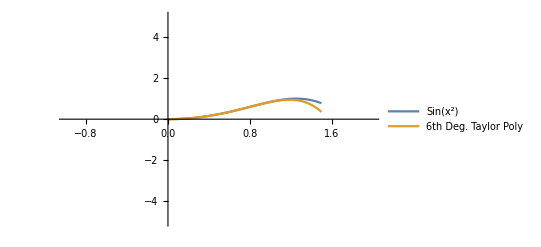

```mathematica
Plot[{func2,expansion3},{x,0,3/2},PlotRange->{{-1,2},{-5,5}}, PlotLegends->{"Sin(x^2)","6th Deg. Taylor Poly"}]
```

This is good, since we can see the the Taylor polynomial closely approximating the true function!

## Problem 3

Use the DSolve command to solve the following two-point boundary value problem:

ϵy’’ + (1+ϵ)y’ + y = 0
	y(0) = 0,
	y(1) = ⅇ^-1

Read the documentation to learn how to plot the solution for different values 0 < ϵ <= 1. Comment on how the solution changes with ϵ.

First, we solve the ODE:

```mathematica
ode = ϵ * y''[x]+ (1 + ϵ) * y'[x] + y[x]==0
y0 = 0;
y1 = ⅇ^-1;
solution = DSolve[{ode,y[0] == y0,y[1]==y1 },y[x],x]
```

y[x]+(1+ϵ) y'[x]+ϵ y''[x]==0

{{y[x]→-(ⅇ^(-x+1/ϵ-x/ϵ) (ⅇ^x-ⅇ^(x/ϵ)))/(-ⅇ+ⅇ^(1/ϵ))}}

To compute the solutions for a different values ϵ, we can use an interactive plot function that allows for adjusting the constants:

```mathematica
Manipulate[Plot[{y[x]/. solution /.ϵ -> θ},{x,0,1},WorkingPrecision->20],
{θ, 0 - 10^-8,1 +10^-8 ,Appearance -> "Labeled"}]
```